# AD_Excitation

## 1D ground state

## useful function

```mathematica
colors = { RGBColor[162/255,37/255,143/255],RGBColor[25/255,169/255,172/255],Orange};Load energy[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]][[-2]]
Load Time Step Energy gnorm[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
```

## Heisenberg

#### relative error-χ

error exponentially-dependent on χ

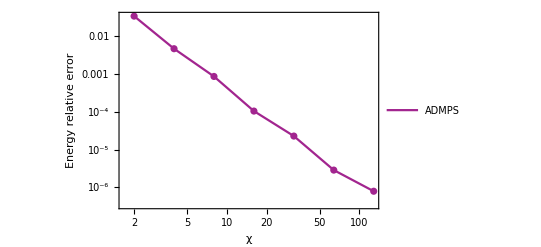

```mathematica
exact=0.25-Log[2];
AD MPS energy=Table[{2^i,Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1.0, 1.0, 1.0)\\D2_χ"<>ToString[2^i]<>".log"]},{i,1,7}];
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
ListLogLogPlot[{AD MPS energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
```

#### relative error-steps

error exponentially-dependent on steps

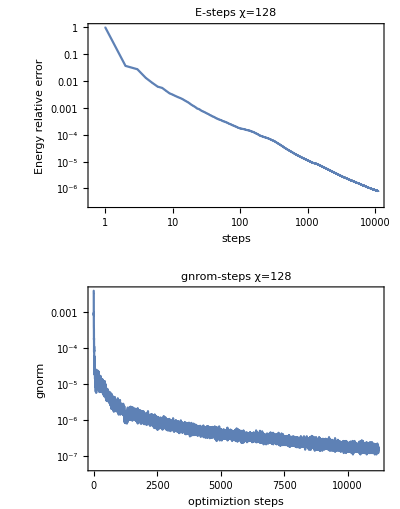

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1.0, 1.0, 1.0)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```

## TFIsing at critical point g=0.5

#### relative error-χ

error exponentially-dependent on χ

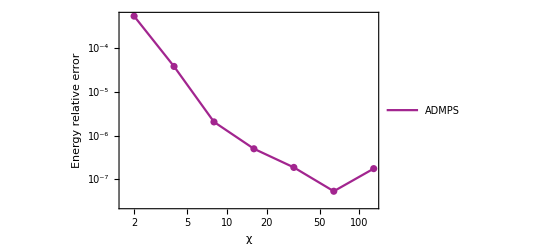

{{2,0.000547469},{4,0.0000384942},{8,2.06229×10^-6},{16,4.99614×10^-7},{32,1.86865×10^-7},{64,5.3171×10^-8},{128,1.75275×10^-7}}

```mathematica
g=1;exact=Integrate[-1/(2Pi)Sqrt[g^2-2g Cos[k]+1],{k,0,2Pi}]/4;
AD MPS energy=Table[{2^i,Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\TFIsing{Float64}(0.5, 0.5)\\D2_χ"<>ToString[2^i]<>".log"]},{i,1,7}];
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
ListLogLogPlot[{AD MPS energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
AD MPS energy aberror
```

#### relative error-steps

error exponentially-dependent on steps

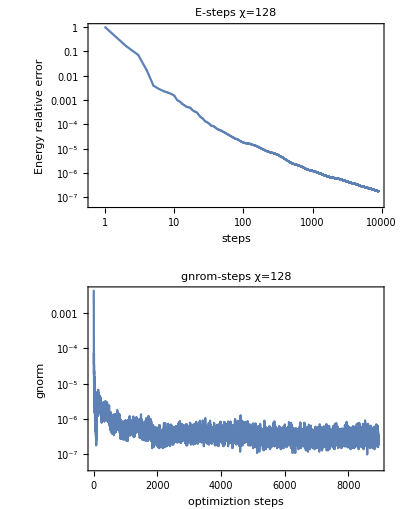

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\TFIsing{Float64}(0.5, 0.5)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```

## 1D Excitation

## U1

```mathematica
U1 = {{0.44214127746903376-0.36649815518214574I,-0.13700868205515632-0.16528649180042596I},{0.1370086836991797+0.1652864904376679I, 0.23346510468812767-0.1935230536660265I}};
U2 = {{Cos[x],-Sin[x]},{Sin[x],Cos[x]}}
```

{{Cos[x],-Sin[x]},{Sin[x],Cos[x]}}

```mathematica
FindRoot[Tr[Transpose[U1].U2]==0,{x,1}]
```

{x→1.5708+0.535137 ⅈ}

```mathematica
U=U2/.{x->1.5707963267948966+0.5351372028447591 ⅈ}
```

{{7.02112×10^-17-0.561047 ⅈ,-1.14664-3.43542×10^-17 ⅈ},{1.14664+3.43542×10^-17 ⅈ,7.02112×10^-17-0.561047 ⅈ}}

```mathematica
FullSimplify[Transpose[U].U]
```

{{1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
ConjugateTranspose[U]
```

{{7.02112×10^-17+0.561047 ⅈ,1.14664-3.43542×10^-17 ⅈ},{-1.14664+3.43542×10^-17 ⅈ,7.02112×10^-17+0.561047 ⅈ}}

## XXZ Δ=1

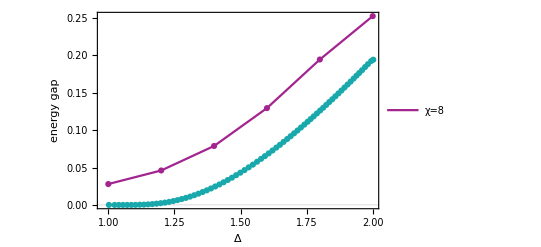

```mathematica
gap={0.05582453026702144,0.09212963838012368,0.15765165546585008,0.25902554676265305,0.38907021917034657,0.5051298373530196}/2;
energy gs=Table[{1.0+0.2(i-1),Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\XXZ{Float64}("<>ToString[NumberForm[1.0+0.2(i-1),{2,1}]]<>")\\D2_χ8.log"]},{i,1,6}];
energy gap=Table[{energy gs[[i,1]],gap[[i]]},{i,1,Length[gap]}];
Exact = Import["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\project\\XXZ_gap.csv"];
ListPlot[{energy gap,Exact },PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=8"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"Δ",None}},ImageSize->400]
```

## Heisenberg S=1/2

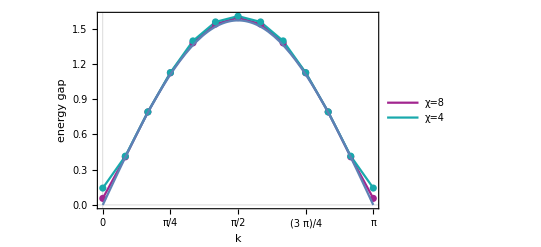

```mathematica
gap1={0.055825535280367065,0.40920812813787655,0.7917343968681471,1.124766271557226,1.379519702559978,1.5398361831063736,1.5948824096077312,1.5398361216280303,1.3795198076975546,1.1247663680286026,0.791734354199969,0.40920812220705727,0.055826048730513896};
gap2={0.143590951236512,0.41530630963142906,0.7919144836295847,1.1263906176088896,1.3962166412387695,1.5578014262286415,1.6073219940962598,1.5578014252762273,1.3962166412329813,1.1263906186752397,0.791914483411365,0.415306313325118,0.14359095621658013};
energy gap1=Table[{Pi/12 (i-1),gap1[[i]]},{i,1,Length[gap1]}];
energy gap2=Table[{Pi/12 (i-1),gap2[[i]]},{i,1,Length[gap2]}];
Show[ListPlot[{energy gap1,energy gap2},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=8","χ=4"},{Scaled[{0.7,0.2}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameTicks->{Automatic,{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],Plot[Pi/2Sin[x],{x,0,Pi}]]
```

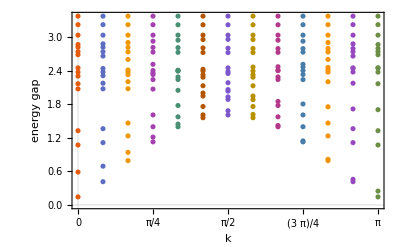

```mathematica
data={{0.143590951236512,0.5870092259712347,1.0707337951983,1.3263344432478805,2.073563850165261,2.165619892294934,2.301621156742532,2.3730666132080156,2.449008197140112,2.683657464312121,2.7384206491358234,2.818365950972775,2.866235940986012,3.0331898497173686,3.2210300244724372,3.37345119341063},{0.41530630963142906,0.6923950873293206,1.1133594753262488,1.3621894933957663,2.0747008336313746,2.174952001918376,2.3087333612536716,2.3749007424076334,2.438143536191836,2.6597089536470033,2.7374261035931426,2.8179389516637525,2.8779344183299473,3.0332219679102903,3.220837632332623,3.3734511934106677},{0.7919144836295847,0.9394372507162686,1.2329967210436572,1.462366914707013,2.0757776686848595,2.2011754004634363,2.3287554801743906,2.3734672856798285,2.410873362626053,2.598776382426956,2.734495616774338,2.8165759690310668,2.9018594525367236,3.0333499923463236,3.220305280550733,3.3734511934106624},{1.1263906176088896,1.2123109469544764,1.3972068921132268,1.6080763343701354,2.070059284275422,2.2390942347697353,2.330343352026295,2.3580473374312225,2.4008230671289366,2.5129076756172792,2.7302487303305463,2.8140843173724517,2.925314954303081,3.033529439724922,3.219561549423882,3.3734511934106144},{1.3962166412387695,1.4443359851707356,1.574289045212467,1.776436756905134,2.0476706202859334,2.2408931583366436,2.286994827586114,2.3914504056329093,2.4004083432737073,2.4064349148543633,2.725841744877775,2.8103262904573456,2.94345495049812,3.033690771114117,3.2187977079862184,3.3734511934106224},{1.5578014262286415,1.6091231958500887,1.7587516674415342,1.9454265622190332,1.9994047821909948,2.12928697743514,2.2828292189764743,2.3258960598628864,2.3925485886916014,2.423346556503682,2.7225843557499445,2.8054828672069165,2.9546955058797835,3.0337928847086504,3.2182250814803877,3.3734511934106},{1.6073219940962598,1.6832041106027977,1.8850907158771646,1.9300425449698047,2.0333231054601573,2.0610987352917878,2.1836917526582567,2.348447840922545,2.382018466256215,2.4487260266357778,2.7213996015857678,2.8002904918059777,2.9584891464456176,3.033826392332483,3.218012524854132,3.3734511934106437},{1.5578014252762273,1.6166731292821443,1.7587516668962289,1.8812511898471822,1.9454265622186104,2.1292869802477616,2.2828292189768686,2.325896084184323,2.3925485838839036,2.4641979564530883,2.7225843509270513,2.7959548057721664,2.954695505879739,3.0337928870610473,3.2182250814803544,3.3734511934106},{1.3962166412329813,1.419289701397628,1.574289048602392,1.7764367569052966,1.8491427897581674,2.2408931602925404,2.2869948650137686,2.400408345154364,2.406434914853967,2.468934025997014,2.7258417353834243,2.793524922969032,2.943454950498195,3.0336907755114226,3.2187977079862917,3.373451193410655},{1.1263906186752397,1.1439354782036188,1.3972069002855398,1.608076334370166,1.8037175067564115,2.2390942832290026,2.3303433482953557,2.400823081277224,2.4651031884563386,2.5129076756172917,2.7302487165032456,2.793152151836493,2.925314954303076,3.0335294456882282,3.219561549423896,3.3734511934106117},{0.791914483411365,0.815703062616672,1.232996732592645,1.4623669147070277,1.7531374417848113,2.2011754610286167,2.3734672619961947,2.4108733996257303,2.457108997069698,2.5987763824269363,2.734495599305844,2.7940380668092204,2.9018594525367267,3.0333499993864415,3.220305280550699,3.3734511934106326},{0.415306313325118,0.45765627295635697,1.1133594888714944,1.3621894933957566,1.7154228382607448,2.174952070270896,2.3749007279721206,2.438143566419825,2.4498476159152482,2.6597089536469856,2.7374260837568563,2.795067512718256,2.8779344183299465,3.03322197562616,3.2208376323326067,3.3734511934106117},{0.14359095621658013,0.24772640617504488,1.0707338104475999,1.3263344432478874,1.7022185454842345,2.1656199633938327,2.3730666017729627,2.446981066016487,2.449008225260004,2.6836574643121374,2.7384206285983876,2.795475532751875,2.86623594098597,3.0331898577235004,3.221030024472387,3.373451193410604}};
energy gap=Table[Transpose@{Table[Pi/12 (i-1),{j,1,16}],data[[i]]},{i,1,Length[data]}];
Show[ListPlot[energy gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->All,PlotStyle->{},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},FrameTicks->{Automatic,{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

## Heisenberg S=1

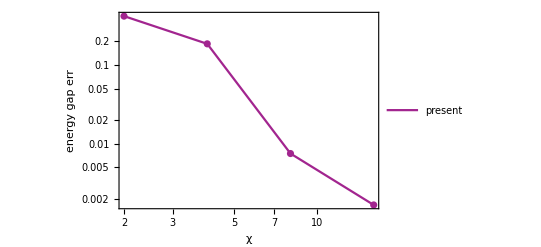

```mathematica
gap={0.5811172937623585,0.4864179655123887,0.40739832778964274,0.40979313525841843};
Verstraete2012=0.410479248463;
energy gap=Table[{2^i,Abs[(gap[[i]]-Verstraete2012)/Verstraete2012]},{i,1,Length[gap]}];
Show[ListLogLogPlot[{energy gap},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"present","Verstraete2012"},{Scaled[{0.6,0.5}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap err",None},{"χ",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],PlotRange->All]
```